Discrete Structures

Operations on Sets

### Overview

Sets can be combined in many different ways.

Set operations are the main tools to make any combination of sets possible.

Many visualizations of those operations are linked to logic.

In this lesson, you will see how to combine sets computationally and visually.

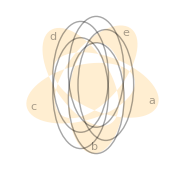

### Union

The union of two sets A and B (A∪B, A||B) is the set obtained by combining the members of each original set.

The closed-form union of sets A_1 through A_n is denoted by ∪_(i=1)^n A_i.

The Union function gives a sorted list containing all the distinct elements that appear in all of the lists:

```mathematica
{1,2,3}∪{3,4,5}
```

{1,2,3,4,5}

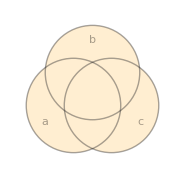

```mathematica
ResourceFunction["VennDiagram"][a||b||c]
```

### Intersection

The intersection of two sets A and B (A∩B, A&&B) is the set of elements common to A and B.

Intersection is a higher priority operation than union.

The closed-form intersection of sets A_1 through A_n is denoted ∩_(i=1)^n A_i.

The Intersection ∩  function gives a sorted list of all elements that are found within all the lists:

```mathematica
{1,2,3}∩{3,4,5}
```

{3}

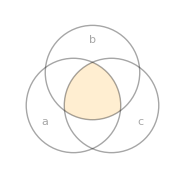

```mathematica
ResourceFunction["VennDiagram"][a&&b&&c]
```

### Complement

The complement (F', F^c, F^-, !F) of a set F is the set of all elements of the domain that are not in F.

The complement is a higher-priority operation than intersection or union.

The Complement function gives the elements in e_all that are not found in any of the e_i:

```mathematica
Complement[Range[7],Range[5,10]]
```

{1,2,3,4}

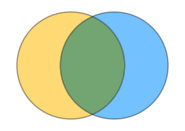

```mathematica
ResourceFunction["VennDiagram"][{Range[7],Range[5,10]}]
```

### Example 1

Consider the sets G, H and I, such that:

```mathematica
{g,h,i}={Range[7],Range[3,9],Range[5,11]}
```

{{1,2,3,4,5,6,7},{3,4,5,6,7,8,9},{5,6,7,8,9,10,11}}

What elements are in (G∪H)∩I'?

```mathematica
(g∪h)∩Complement[Range[11],i]
```

{1,2,3,4}

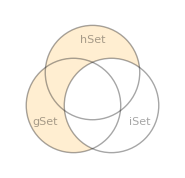

```mathematica
ResourceFunction["VennDiagram"][(gSet||hSet)∧!iSet]
```

### Example 2

Consider the sets G, H and I, such that:

```mathematica
{g,h,i}={Range[7],Range[3,9],Range[5,11]}
```

{{1,2,3,4,5,6,7},{3,4,5,6,7,8,9},{5,6,7,8,9,10,11}}

What part of the Venn diagram of G,H,I contains no elements?

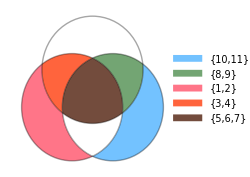

```mathematica
ResourceFunction["VennDiagram"][{g,h,i}]
```

It is G∩I∩H'∪G'∩I'∩H.

### Set Identities

```mathematica
Grid[{{"Identity",{"A∩U=A","A∪∅=A"}},{"Domination",{"A∪U=U","A∩∅=∅"}},{"Idempotency",{"A∪A=A","A∩A=A"}},{"Complementation",{"(A')'=A"}},{"Commutativity",{"A∪B=B∪A","A∩B=B∩A"}},{"Associativity",{"A∪(B∪C)=(A∪B)∪C","A∩(B∩C)=(A∩B)∩C"}},{"Distributivity",{"A∪(B∩C)=(A∪B)∩(A∪C)","A∩(B∪C)=A∩B∪A∩B"}},{"De Morgan's",{"(A∩B)'=A'∪B'","(A∪B)'=A'∩B'"}},{"Absorption",{"A∪(A∩B)=A","A∩(A∪B)=A"}},{"Complement",{"A∪A'=U","A∩A'=∅"}}},Frame->All]
```

Identity | {A∩U=A,A∪∅=A}
Domination | {A∪U=U,A∩∅=∅}
Idempotency | {A∪A=A,A∩A=A}
Complementation | {(A')'=A}
Commutativity | {A∪B=B∪A,A∩B=B∩A}
Associativity | {A∪(B∪C)=(A∪B)∪C,A∩(B∩C)=(A∩B)∩C}
Distributivity | {A∪(B∩C)=(A∪B)∩(A∪C),A∩(B∪C)=A∩B∪A∩B}
De Morgan's | {(A∩B)'=A'∪B',(A∪B)'=A'∩B'}
Absorption | {A∪(A∩B)=A,A∩(A∪B)=A}
Complement | {A∪A'=U,A∩A'=∅}

You can prove any of these identities using Venn diagrams:

```mathematica
dict=<|"Identity"->{a&&(U||!U),a||(∅&&!∅)},"Domination"->{a||(U||!U),a&&(∅&&!∅)},"Idempotency"->{{{a},{a}}},"Commutativity"->{a||b,a&&b},"Associativity"->{a||b||c,a&&b&&c},"Distributivity"->{a||(b&&c),a&&(b||c)},"De Morgan's"->{!(a&&b),!(a||b)},"Absorption"->{a||(a&&b),a&&(a||b)}|>;
Manipulate[Table[ResourceFunction["VennDiagram"][law],{law,dict[lawname]}],{lawname,Keys[dict]},SaveDefinitions->True]
```

### Membership Tables

Notice the direct correspondence between set identities and logic.

Any identity could be proven using a truth table:

(A∩B)'=A'∪B'

```mathematica
ResourceFunction["TruthTable"][{!(A&&B),!A||!B},{A,B}]
```

A | B | !(A&&B) | !A||!B
True | True | False | False
True | False | True | True
False | True | True | True
False | False | True | True

### Example

Show (A∩B∪C∪D)∩B'∪C is equivalent to B'∩D∪C using a Venn diagram and a membership table:

```mathematica
equ={(a∧b∨c∨d)∧!b∨c,(¬b∧d)∨c}
```

{(((a&&b)||c||d)&&!b)||c,(!b&&d)||c}

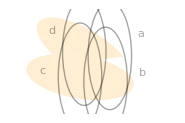
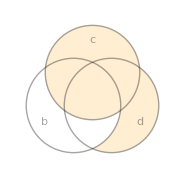

```mathematica
ResourceFunction["VennDiagram"]/@equ
```

```mathematica
ResourceFunction["TruthTable"][equ,{a,b,c,d}]
```

a | b | c | d | (((a&&b)||c||d)&&!b)||c | (!b&&d)||c
True | True | True | True | True | True
True | True | True | False | True | True
True | True | False | True | False | False
True | True | False | False | False | False
True | False | True | True | True | True
True | False | True | False | True | True
True | False | False | True | True | True
True | False | False | False | False | False
False | True | True | True | True | True
False | True | True | False | True | True
False | True | False | True | False | False
False | True | False | False | False | False
False | False | True | True | True | True
False | False | True | False | True | True
False | False | False | True | True | True
False | False | False | False | False | False

### Summary

Sets can be combined using the union (∪, ||), intersection (∩, &&) and complement (’, !) operations.

Set identities help simplify set expressions.

There is an equivalence between logic and set identities.

Visualization is possible using tools like Venn diagrams and membership tables.

All these operations can be combined into more powerful tools, commonly called functions.

Download Notebook »